## Cylinder

All the calculations below make heavily use of the fact that P[R2-R1] the two-point probability distribution of two vectors connecting two points being e.g. inside the cylinder, on the ends, on the hull, or .. can be stated as a convolution of two one-point correlation functions going from the center to R1 and from the centre to R2, where we choose the center of the cylinder as origo of our coordinate system. In Fourier space, the two-point probability distribution is just the product of the two one-point correlation functions. Although we have to take care of an additional average over the direction from which the q-vector hits the cylinder.

```mathematica
$Assumptions:={R>0, q>0,L>0,r>0,θq> 0,θq<= π/2}
```

To integrate a cylinder we choose cylindrical coordinates putting the cylinder symmetry axis along the z axis . Again we can place the q vector anywhere in the upper xz plane due to rotational symmetry .

```mathematica
Rvec:={r Cos[ϕ],r Sin[ϕ],z}
```

```mathematica
qvec:={q Sin[θq],0,q Cos[θq]}
```

```mathematica
Rvec.qvec
```

q z Cos[θq]+q r Cos[ϕ] Sin[θq]

Normalization is the volume of the cylinder :

```mathematica
Integrate[ r,{r,0,R},{ϕ,-π,π},{z,-L/2,L/2}]
```

L π R^2

The form factor amplitude of all scatterers relative to the center (at the origin) is then for fixed q vector

```mathematica
FFA=Integrate[Exp[I Rvec.qvec] r,{r,0,R},{ϕ,-π,π},{z,-L/2,L/2}]/(L π R^2)
```

(4 BesselJ[1,q R Sin[θq]] Csc[θq] Sec[θq] Sin[1/2 L q Cos[θq]])/(L q^2 R)

Doing the average over the direction of the q vector, since the cylinder is rotationally invariant . The integral can not be performed analytically.

```mathematica
Fcylinder=Integrate[FFA^2 Sin[θq],{θq,0,π/2}]
```

∫_0^(π/2) (16 BesselJ[1,q R Sin[θq]]^2 Csc[θq] Sec[θq]^2 Sin[1/2 L q Cos[θq]]^2)/(L^2 q^4 R^2)ⅆθq

Ref : G . Fournet, Bull . Soc . Fr . Mineral . Crist ., 74 (1951) 39 - 113.
To calculate the phase factor between the centre point and any point on the round hull of the cyllinder, we differentiate. Note that we still need to perform the orientational average for all the expressions below.

```mathematica
Psicenter2hull=D[FFA (L π R^2),R]/(L 2π R)//FullSimplify
```

(2 BesselJ[0,q R Sin[θq]] Sec[θq] Sin[1/2 L q Cos[θq]])/(L q)

```mathematica
Psicenter2hull/.L->y/q/.R->x/q/.θq-> t//CForm//Simplify
```

(2*BesselJ(0,x*Sin(t))*Sec(t)*Sin((y*Cos(t))/2.))/y

```mathematica
Psihull2hull=Psicenter2hull^2 //FullSimplify
```

(4 BesselJ[0,q R Sin[θq]]^2 Sec[θq]^2 Sin[1/2 L q Cos[θq]]^2)/(L^2 q^2)

```mathematica
Ahull=Psicenter2hull FFA  //FullSimplify
```

(8 BesselJ[0,q R Sin[θq]] BesselJ[1,q R Sin[θq]] Csc[θq] Sec[θq]^2 Sin[1/2 L q Cos[θq]]^2)/(L^2 q^3 R)

Phase factor from center to a point on the circular cross-section at z.

```mathematica
Psicenter2endz[z_]=Integrate[Exp[I Rvec.qvec] r,{r,0,R},{ϕ,-π,π}]/( π R^2)// FunctionExpand
```

(2 ⅇ^(ⅈ q z Cos[θq]) BesselJ[1,q R Sin[θq]] Csc[θq])/(q R)

Phase factor from center to a point on one of the two circular cross-sections at L/2, -L/2.

```mathematica
Psicenter2ends=(Psicenter2endz[L/2]+Psicenter2endz[-L/2])/2//FullSimplify
```

Cos[1/2 L q Cos[θq]] Hypergeometric0F1Regularized[2,-1/4 q^2 R^2 Sin[θq]^2]

```mathematica
Psicenter2ends/.L->y/q/.R->x/q/.θq-> t//CForm//Simplify
```

Cos((y*Cos(t))/2.)*Hypergeometric0F1Regularized(2,-0.25*(Power(x,2)*Power(Sin(t),2)))

```mathematica
Psiend2end=Psicenter2ends Psicenter2ends//FullSimplify
```

Cos[1/2 L q Cos[θq]]^2 Hypergeometric0F1Regularized[2,-1/4 q^2 R^2 Sin[θq]^2]^2

```mathematica
Aends=Psicenter2ends FFA //FullSimplify
```

(4 BesselJ[1,q R Sin[θq]]^2 Csc[θq]^2 Sec[θq] Sin[L q Cos[θq]])/(L q^3 R^2)

```mathematica
Psiend2hull=Psicenter2ends Psicenter2hull//FullSimplify
```

(2 BesselJ[0,q R Sin[θq]] BesselJ[1,q R Sin[θq]] Csc[θq] Sec[θq] Sin[L q Cos[θq]])/(L q^2 R)

```mathematica
Psicenter2surface=(2 π R^2Psicenter2ends+2π R L Psicenter2hull)/(2π R L+2 π R^2)//FullSimplify
```

1/(q (L+R))2 (BesselJ[1,q R Sin[θq]] Cos[1/2 L q Cos[θq]] Csc[θq]+BesselJ[0,q R Sin[θq]] Sec[θq] Sin[1/2 L q Cos[θq]])

#### Comparing to sampled data and saving data for validation:

```mathematica
PARENTDIR=Directory[]
```

/home/zqex/source/SEB/Mathematica

```mathematica
Clear[DIR1,DIR2,DIRO1,DIRO2]
DIR1:=PARENTDIR<>"/Sampled/SolidCylinder_R1.000000_L1.500000/"
DIR2:=PARENTDIR<>"/Sampled/SolidCylinder_R2.000000_L0.500000/"
DIRO1:=PARENTDIR<>"/../Examples/Validation/SolidCylinder_R1_L1.5/"
DIRO2:=PARENTDIR<>"/../Examples/Validation/SolidCylinder_R2_L0.5/"
CreateDirectory[DIRO1];
CreateDirectory[DIRO2];
```

CreateDirectory::eexist: /home/zqex/source/SEB/Examples/Validation/SolidCylinder_mathematica_R1_L1.5/ already exists.

CreateDirectory::eexist: /home/zqex/source/SEB/Examples/Validation/SolidCylinder_mathematica_R2_L0.5/ already exists.

```mathematica
SaveFunction[func_,filename_,NN_,qmin_,qmax_]:=Module[{},Export[filename,{#,N[func[#]]}&/@Table[10^(Log[10,qmax/qmin]*i/NN+Log[10,qmin]),{i,0,NN}]]]
SetAttributes[SaveFunction,HoldAll]
```

```mathematica
Clear[qvec,qq]
qvec[qmin_,qmax_,NN_]:=Table[10^(Log[10,qmax/qmin]*i/NN+Log[10,qmin]),{i,0,NN}]
qq:=qvec[0.8,50,500]//N
```

#### Form factor :

(16 BesselJ[1,q R Sin[θq]]^2 Csc[θq]^2 Sec[θq]^2 Sin[1/2 L q Cos[θq]]^2)/(L^2 q^4 R^2)

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidCylinder_mathematica_R1_L1.5/F.dat

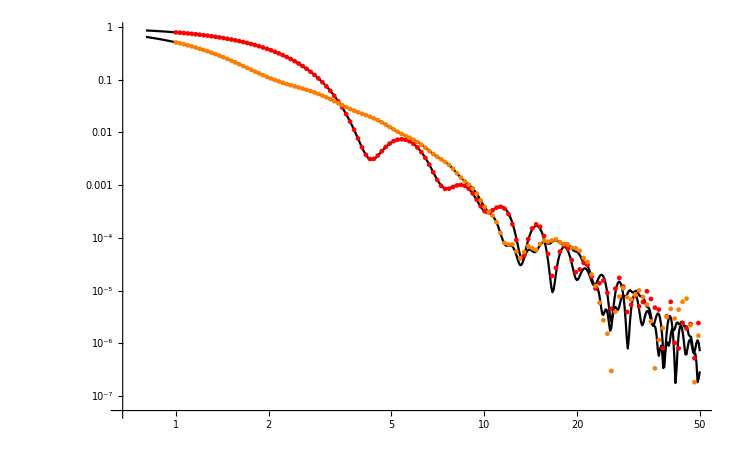

```mathematica
Clear[Term,Func1,Func2,DATA1,DATA2,OFILE,DATA1,DATA2]
Term[q_]=FFA^2
FILE="FF.q";
OFILE="F.dat";
DIRO1<>OFILE
Func1[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 1/.L-> 1.5,{θq,0,π/2}]
Func2[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 2/.L-> 0.5,{θq,0,π/2}]
SaveFunction[Func1,DIRO1<>OFILE,200,0.01,50];
SaveFunction[Func2,DIRO2<>OFILE,200,0.01,50];
DATA1={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
DATA2={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR2<>FILE,"Table"],1];
ListLogLogPlot[{DATA1,DATA2,{# ,Abs[Func1[#]]}&/@qq,{#,Abs[Func2[#]]}&/@qq},PlotStyle->{{Red,Thick},{Orange,Thick}, Black,Black},Joined-> {False,False,True,True}]
```

```mathematica
Solve[Collect[Integrate[Series[Term[q],{q,0,3}]Sin[θq],{θq,0,π/2}],q]==1-(q^2 Rg2)/3,Rg2]//Simplify
```

{{Rg2→1/12 (L^2+6 R^2)}}

```mathematica
Term[q]/.L->y/q/.R->x/q/.θq-> t//CForm
```

(16*Power(BesselJ(1,x*Sin(t)),2)*Power(Csc(t),2)*Power(Sec(t),2)*Power(Sin((y*Cos(t))/2.),2))/
   (Power(x,2)*Power(y,2))

#### Form factor Amplitude relative to center:

(4 BesselJ[1,q R Sin[θq]] Csc[θq] Sec[θq] Sin[1/2 L q Cos[θq]])/(L q^2 R)

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidCylinder_mathematica_R1_L1.5/FFA_center.dat

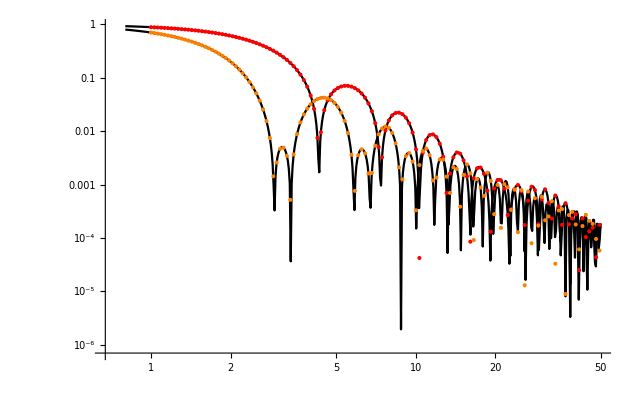

```mathematica
Clear[Term,Func1,Func2,DATA1,DATA2,OFILE,DATA1,DATA2]
Term[q_]=FFA
FILE="FFA_center.q";
OFILE="FFA_center.dat";
DIRO1<>OFILE
Func1[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 1/.L-> 1.5,{θq,0,π/2}]
Func2[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 2/.L-> 0.5,{θq,0,π/2}]
SaveFunction[Func1,DIRO1<>OFILE,200,0.01,50];
SaveFunction[Func2,DIRO2<>OFILE,200,0.01,50];
DATA1={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
DATA2={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR2<>FILE,"Table"],1];
ListLogLogPlot[{DATA1,DATA2,{# ,Abs[Func1[#]]}&/@qq,{#,Abs[Func2[#]]}&/@qq},PlotStyle->{{Red,Thick},{Orange,Thick}, Black,Black},Joined-> {False,False,True,True}]
```

```mathematica
Solve[Collect[Integrate[Series[Term[q],{q,0,3}]Sin[θq],{θq,0,π/2}],q]==1-(q^2 sR2)/6,sR2]//Simplify
```

{{sR2→1/12 (L^2+6 R^2)}}

```mathematica
Term[q]/.L->y/q/.R->x/q/.θq-> t//CForm//Simplify
```

(4*BesselJ(1,x*Sin(t))*Csc(t)*Sec(t)*Sin((y*Cos(t))/2.))/(x*y)

#### Form factor Amplitude relative to hull:

(8 BesselJ[0,q R Sin[θq]] BesselJ[1,q R Sin[θq]] Csc[θq] Sec[θq]^2 Sin[1/2 L q Cos[θq]]^2)/(L^2 q^3 R)

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidCylinder_mathematica_R1_L1.5/FFA_hull.dat

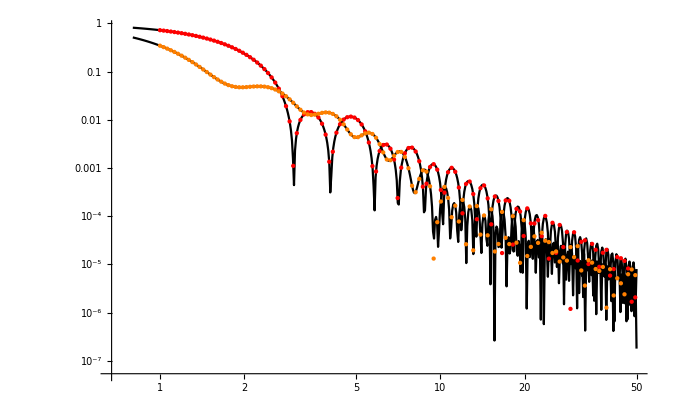

```mathematica
Clear[Term,Func1,Func2,DATA1,DATA2,OFILE,DATA1,DATA2]
Term[q_]=FFA Psicenter2hull
FILE="FFA_hull.q";
OFILE="FFA_hull.dat";
DIRO1<>OFILE
Func1[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 1/.L-> 1.5,{θq,0,π/2}]
Func2[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 2/.L-> 0.5,{θq,0,π/2}]
SaveFunction[Func1,DIRO1<>OFILE,200,0.01,50];
SaveFunction[Func2,DIRO2<>OFILE,200,0.01,50];
DATA1={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
DATA2={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR2<>FILE,"Table"],1];
ListLogLogPlot[{DATA1,DATA2,{# ,Abs[Func1[#]]}&/@qq,{#,Abs[Func2[#]]}&/@qq},PlotStyle->{{Red,Thick},{Orange,Thick}, Black,Black},Joined-> {False,False,True,True}]
```

#### Form factor Amplitude relative to ends:

1/(L q^2 R)4 BesselJ[1,q R Sin[θq]] Cos[1/2 L q Cos[θq]] Csc[θq] Hypergeometric0F1Regularized[2,-1/4 q^2 R^2 Sin[θq]^2] Sec[θq] Sin[1/2 L q Cos[θq]]

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidCylinder_mathematica_R1_L1.5/FFA_ends.dat

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θq near {θq} = {1.5708}. NIntegrate obtained -0.0000228683 and 5.29061×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θq near {θq} = {1.5708}. NIntegrate obtained -0.0000187586 and 3.85135×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θq near {θq} = {1.5708}. NIntegrate obtained -5.75476×10^-6 and 3.54882×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θq near {θq} = {1.5708}. NIntegrate obtained 1.09237×10^-6 and 1.66631×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θq near {θq} = {1.5708}. NIntegrate obtained -0.0000103871 and 3.55518×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θq near {θq} = {1.5708}. NIntegrate obtained -0.0000130573 and 5.1784×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

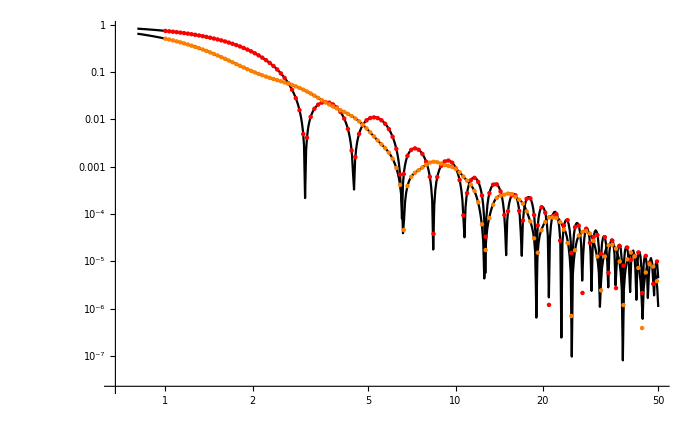

```mathematica
Clear[Term,Func1,Func2,DATA1,DATA2,OFILE,DATA1,DATA2]
Term[q_]=FFA Psicenter2ends
FILE="FFA_end.q";
OFILE="FFA_ends.dat";
DIRO1<>OFILE
Func1[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 1/.L-> 1.5,{θq,0,π/2}]
Func2[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 2/.L-> 0.5,{θq,0,π/2}]
SaveFunction[Func1,DIRO1<>OFILE,200,0.01,50];
SaveFunction[Func2,DIRO2<>OFILE,200,0.01,50];
DATA1={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
DATA2={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR2<>FILE,"Table"],1];
ListLogLogPlot[{DATA1,DATA2,{# ,Abs[Func1[#]]}&/@qq,{#,Abs[Func2[#]]}&/@qq},PlotStyle->{{Red,Thick},{Orange,Thick}, Black,Black},Joined-> {False,False,True,True}]
```

```mathematica
Solve[Collect[Integrate[Series[Term[q],{q,0,3}]Sin[θq],{θq,0,π/2}],q]==1-(q^2 sR2)/6,sR2]//Simplify
```

{{sR2→L^2/3+R^2}}

#### Form factor amplitude relative to surface:

1/(L q^3 R (L+R))8 BesselJ[1,q R Sin[θq]] Csc[θq] Sec[θq] Sin[1/2 L q Cos[θq]] (BesselJ[1,q R Sin[θq]] Cos[1/2 L q Cos[θq]] Csc[θq]+BesselJ[0,q R Sin[θq]] Sec[θq] Sin[1/2 L q Cos[θq]])

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidCylinder_mathematica_R1_L1.5/FFA_surface.dat

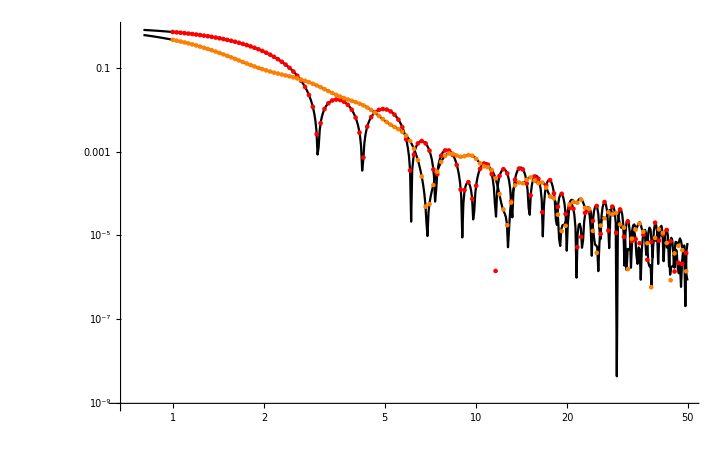

```mathematica
Clear[Term,Func1,Func2,DATA1,DATA2,OFILE,DATA1,DATA2]
Term[q_]=FFA Psicenter2surface
FILE="FFA_surface.q";
OFILE="FFA_surface.dat";
DIRO1<>OFILE
Func1[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 1/.L-> 1.5,{θq,0,π/2}]
Func2[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 2/.L-> 0.5,{θq,0,π/2}]
SaveFunction[Func1,DIRO1<>OFILE,200,0.01,50];
SaveFunction[Func2,DIRO2<>OFILE,200,0.01,50];
DATA1={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
DATA2={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR2<>FILE,"Table"],1];
ListLogLogPlot[{DATA1,DATA2,{# ,Abs[Func1[#]]}&/@qq,{#,Abs[Func2[#]]}&/@qq},PlotStyle->{{Red,Thick},{Orange,Thick}, Black,Black},Joined-> {False,False,True,True}]
```

```mathematica
Solve[Collect[Integrate[Series[Term[q],{q,0,3}]Sin[θq],{θq,0,π/2}],q]==1-(q^2 sR2)/6,sR2]//Simplify
```

{{sR2→(L^3+2 L^2 R+9 L R^2+6 R^3)/(6 (L+R))}}

#### Phase factor center to end:

Cos[1/2 L q Cos[θq]] Hypergeometric0F1Regularized[2,-1/4 q^2 R^2 Sin[θq]^2]

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidCylinder_mathematica_R1_L1.5/PF_center2ends.dat

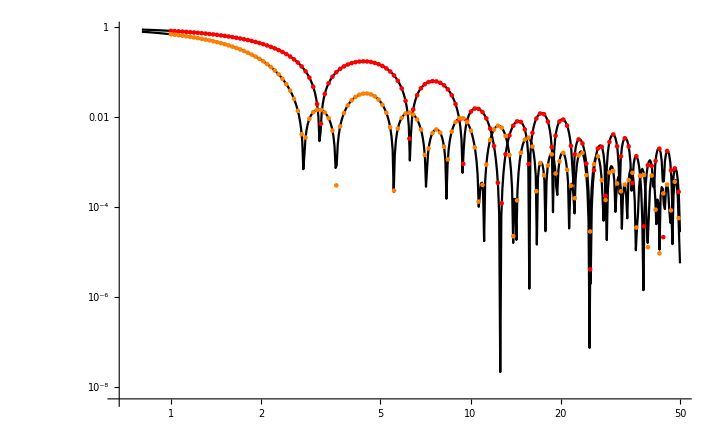

```mathematica
Clear[Term,Func1,Func2,DATA1,DATA2,OFILE,DATA1,DATA2]
Term[q_]=Psicenter2ends//FullSimplify
FILE="PF_center_end.q";
OFILE="PF_center2ends.dat";
DIRO1<>OFILE
Func1[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 1/.L-> 1.5,{θq,0,π/2}]
Func2[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 2/.L-> 0.5,{θq,0,π/2}]
SaveFunction[Func1,DIRO1<>OFILE,200,0.01,50];
SaveFunction[Func2,DIRO2<>OFILE,200,0.01,50];
DATA1={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
DATA2={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR2<>FILE,"Table"],1];
ListLogLogPlot[{DATA1,DATA2,{# ,Abs[Func1[#]]}&/@qq,{#,Abs[Func2[#]]}&/@qq},PlotStyle->{{Red,Thick},{Orange,Thick}, Black,Black},Joined-> {False,False,True,True}]
```

```mathematica
Solve[Collect[Integrate[Series[Term[q],{q,0,3}]Sin[θq],{θq,0,π/2}],q]==1-(q^2 sR2)/6,sR2]//Simplify
```

{{sR2→1/4 (L^2+2 R^2)}}

#### Phase factor center to hull:

(2 BesselJ[0,q R Sin[θq]] Sec[θq] Sin[1/2 L q Cos[θq]])/(L q)

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidCylinder_mathematica_R1_L1.5/PF_center2hull.dat

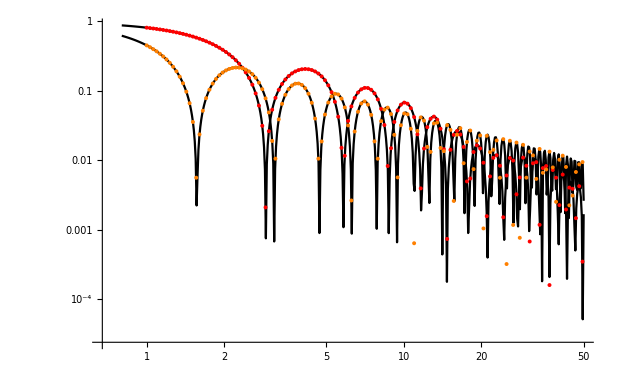

```mathematica
Clear[Term,Func1,Func2,DATA1,DATA2,OFILE,DATA1,DATA2]
Term[q_]= Psicenter2hull//FullSimplify
FILE="PF_center_hull.q";
OFILE="PF_center2hull.dat";
DIRO1<>OFILE
Func1[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 1/.L-> 1.5,{θq,0,π/2}]
Func2[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 2/.L-> 0.5,{θq,0,π/2}]
SaveFunction[Func1,DIRO1<>OFILE,200,0.01,50];
SaveFunction[Func2,DIRO2<>OFILE,200,0.01,50];
DATA1={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
DATA2={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR2<>FILE,"Table"],1];
ListLogLogPlot[{DATA1,DATA2,{# ,Abs[Func1[#]]}&/@qq,{#,Abs[Func2[#]]}&/@qq},PlotStyle->{{Red,Thick},{Orange,Thick}, Black,Black},Joined-> {False,False,True,True}]
```

```mathematica
Solve[Collect[Integrate[Series[Term[q],{q,0,3}]Sin[θq],{θq,0,π/2}],q]==1-(q^2 sR2)/6,sR2]//Simplify
```

{{sR2→L^2/12+R^2}}

#### Phase factor center to surface:

1/(q (L+R))2 (BesselJ[1,q R Sin[θq]] Cos[1/2 L q Cos[θq]] Csc[θq]+BesselJ[0,q R Sin[θq]] Sec[θq] Sin[1/2 L q Cos[θq]])

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidCylinder_mathematica_R1_L1.5/PF_center2surface.dat

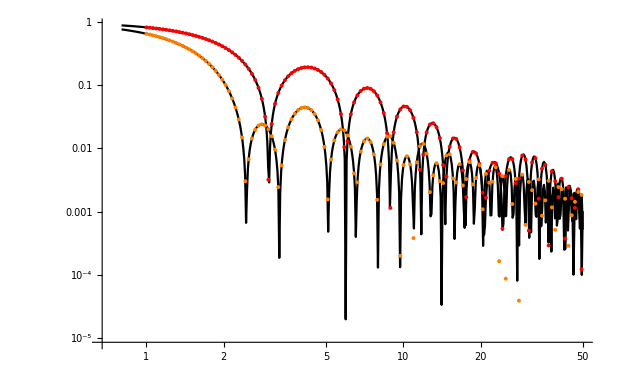

```mathematica
Clear[Term,Func1,Func2,DATA1,DATA2,OFILE,DATA1,DATA2]
Term[q_]=  Psicenter2surface//FullSimplify
FILE="PF_center_surface.q";
OFILE="PF_center2surface.dat";
DIRO1<>OFILE
Func1[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 1/.L-> 1.5,{θq,0,π/2}]
Func2[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 2/.L-> 0.5,{θq,0,π/2}]
SaveFunction[Func1,DIRO1<>OFILE,200,0.01,50];
SaveFunction[Func2,DIRO2<>OFILE,200,0.01,50];
DATA1={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
DATA2={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR2<>FILE,"Table"],1];
ListLogLogPlot[{DATA1,DATA2,{# ,Abs[Func1[#]]}&/@qq,{#,Abs[Func2[#]]}&/@qq},PlotStyle->{{Red,Thick},{Orange,Thick}, Black,Black},Joined-> {False,False,True,True}]
```

```mathematica
Solve[Collect[Integrate[Series[Term[q],{q,0,3}]Sin[θq],{θq,0,π/2}],q]==1-(q^2 sR2)/6,sR2]//Simplify
```

{{sR2→(L^3+3 L^2 R+12 L R^2+6 R^3)/(12 (L+R))}}

#### Phase factor end to end:

Cos[1/2 L q Cos[θq]]^2 Hypergeometric0F1Regularized[2,-1/4 q^2 R^2 Sin[θq]^2]^2

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidCylinder_mathematica_R1_L1.5/PF_end2end.dat

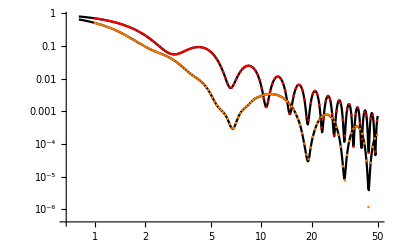

```mathematica
Clear[Term,Func1,Func2,DATA1,DATA2,OFILE,DATA1,DATA2]
Term[q_]= Psicenter2ends Psicenter2ends //FullSimplify
FILE="PF_end_end.q";
OFILE="PF_end2end.dat";
DIRO1<>OFILE
Func1[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 1/.L-> 1.5,{θq,0,π/2}]
Func2[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 2/.L-> 0.5,{θq,0,π/2}]
SaveFunction[Func1,DIRO1<>OFILE,200,0.01,50];
SaveFunction[Func2,DIRO2<>OFILE,200,0.01,50];
DATA1={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
DATA2={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR2<>FILE,"Table"],1];
ListLogLogPlot[{DATA1,DATA2,{# ,Abs[Func1[#]]}&/@qq,{#,Abs[Func2[#]]}&/@qq},PlotStyle->{{Red,Thick},{Orange,Thick}, Black,Black},Joined-> {False,False,True,True}]
```

```mathematica
Solve[Collect[Integrate[Series[Term[q],{q,0,3}]Sin[θq],{θq,0,π/2}],q]==1-(q^2 sR2)/6,sR2]//Simplify
```

{{sR2→L^2/2+R^2}}

#### Phase factor end to hull:

(2 BesselJ[0,q R Sin[θq]] BesselJ[1,q R Sin[θq]] Csc[θq] Sec[θq] Sin[L q Cos[θq]])/(L q^2 R)

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidCylinder_mathematica_R1_L1.5/PF_end2hull.dat

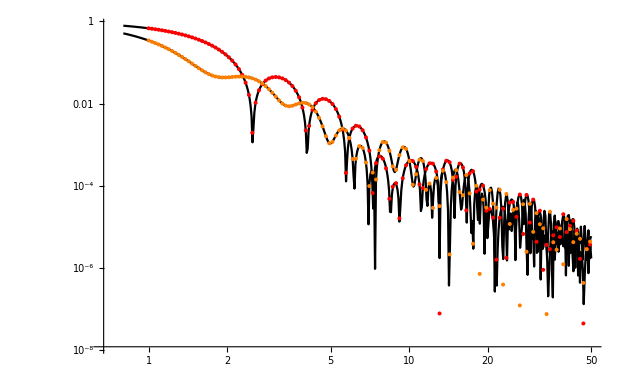

```mathematica
Clear[Term,Func1,Func2,DATA1,DATA2,OFILE,DATA1,DATA2]
Term[q_]= Psicenter2ends Psicenter2hull //FullSimplify
FILE="PF_end_hull.q";
OFILE="PF_end2hull.dat";
DIRO1<>OFILE
Func1[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 1/.L-> 1.5,{θq,0,π/2}]
Func2[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 2/.L-> 0.5,{θq,0,π/2}]
SaveFunction[Func1,DIRO1<>OFILE,200,0.01,50];
SaveFunction[Func2,DIRO2<>OFILE,200,0.01,50];
DATA1={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
DATA2={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR2<>FILE,"Table"],1];
ListLogLogPlot[{DATA1,DATA2,{# ,Abs[Func1[#]]}&/@qq,{#,Abs[Func2[#]]}&/@qq},PlotStyle->{{Red,Thick},{Orange,Thick}, Black,Black},Joined-> {False,False,True,True}]
```

```mathematica
Solve[Collect[Integrate[Series[Term[q],{q,0,3}]Sin[θq],{θq,0,π/2}],q]==1-(q^2 sR2)/6,sR2]//Simplify
```

{{sR2→1/6 (2 L^2+9 R^2)}}

#### Phase factor end to surface:

1/(q (L+R))2 Cos[1/2 L q Cos[θq]]^2 Hypergeometric0F1Regularized[2,-1/4 q^2 R^2 Sin[θq]^2] (BesselJ[1,q R Sin[θq]] Csc[θq]+BesselJ[0,q R Sin[θq]] Sec[θq] Tan[1/2 L q Cos[θq]])

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidCylinder_mathematica_R1_L1.5/PF_end2surface.dat

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θq near {θq} = {0.0337476}. NIntegrate obtained 1.19474×10^-6 and 9.62987×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θq near {θq} = {0.929592}. NIntegrate obtained 3.61768×10^-6 and 8.83723×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θq near {θq} = {1.37445}. NIntegrate obtained 4.9684×10^-6 and 3.49905×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θq near {θq} = {1.37445}. NIntegrate obtained 0.0000122244 and 2.32873×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

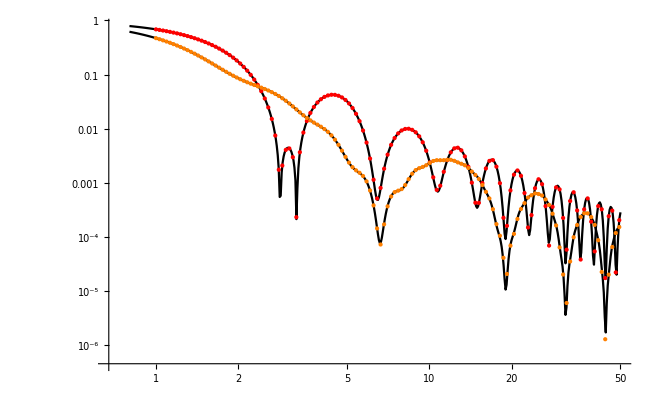

```mathematica
Clear[Term,Func1,Func2,DATA1,DATA2,OFILE,DATA1,DATA2]
Term[q_]= Psicenter2ends Psicenter2surface //FullSimplify
FILE="PF_end_surface.q";
OFILE="PF_end2surface.dat";
DIRO1<>OFILE
Func1[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 1/.L-> 1.5,{θq,0,π/2}]
Func2[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 2/.L-> 0.5,{θq,0,π/2}]
SaveFunction[Func1,DIRO1<>OFILE,200,0.01,50];
SaveFunction[Func2,DIRO2<>OFILE,200,0.01,50];
DATA1={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
DATA2={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR2<>FILE,"Table"],1];
ListLogLogPlot[{DATA1,DATA2,{# ,Abs[Func1[#]]}&/@qq,{#,Abs[Func2[#]]}&/@qq},PlotStyle->{{Red,Thick},{Orange,Thick}, Black,Black},Joined-> {False,False,True,True}]
```

```mathematica
Solve[Collect[Integrate[Series[Term[q],{q,0,3}]Sin[θq],{θq,0,π/2}],q]==1-(q^2 sR2)/6,sR2]//Simplify
```

{{sR2→(2 L^3+3 L^2 R+9 L R^2+6 R^3)/(6 (L+R))}}

#### Phase hull end to hull:

(4 BesselJ[0,q R Sin[θq]]^2 Sec[θq]^2 Sin[1/2 L q Cos[θq]]^2)/(L^2 q^2)

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidCylinder_mathematica_R1_L1.5/PF_hull2hull.dat

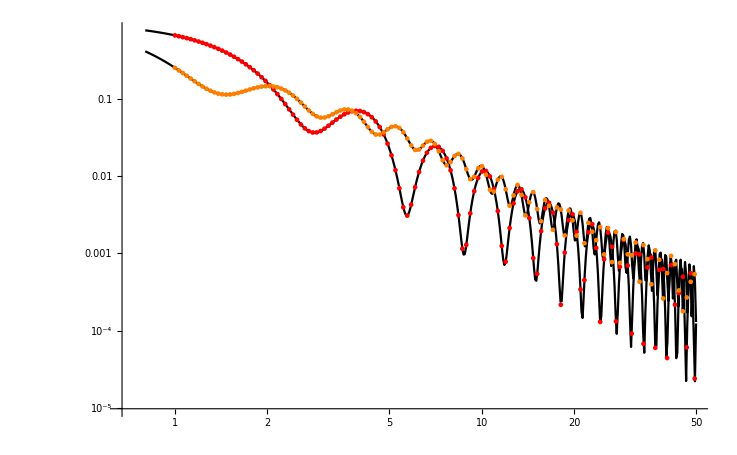

```mathematica
Clear[Term,Func1,Func2,DATA1,DATA2,OFILE,DATA1,DATA2]
Term[q_]= Psicenter2hull^2//FullSimplify
FILE="PF_hull_hull.q";
OFILE="PF_hull2hull.dat";
DIRO1<>OFILE
Func1[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 1/.L-> 1.5,{θq,0,π/2}]
Func2[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 2/.L-> 0.5,{θq,0,π/2}]
SaveFunction[Func1,DIRO1<>OFILE,200,0.01,50];
SaveFunction[Func2,DIRO2<>OFILE,200,0.01,50];
DATA1={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
DATA2={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR2<>FILE,"Table"],1];
ListLogLogPlot[{DATA1,DATA2,{# ,Abs[Func1[#]]}&/@qq,{#,Abs[Func2[#]]}&/@qq},PlotStyle->{{Red,Thick},{Orange,Thick}, Black,Black},Joined-> {False,False,True,True}]
```

```mathematica
Solve[Collect[Integrate[Series[Term[q],{q,0,3}]Sin[θq],{θq,0,π/2}],q]==1-(q^2 sR2)/6,sR2]//Simplify
```

{{sR2→L^2/6+2 R^2}}

#### Phase hull end to surface:

1/(L q^2 (L+R))2 BesselJ[0,q R Sin[θq]] Sec[θq] (-BesselJ[0,q R Sin[θq]] (-1+Cos[L q Cos[θq]]) Sec[θq]+BesselJ[1,q R Sin[θq]] Csc[θq] Sin[L q Cos[θq]])

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidCylinder_mathematica_R1_L1.5/PF_hull2surface.dat

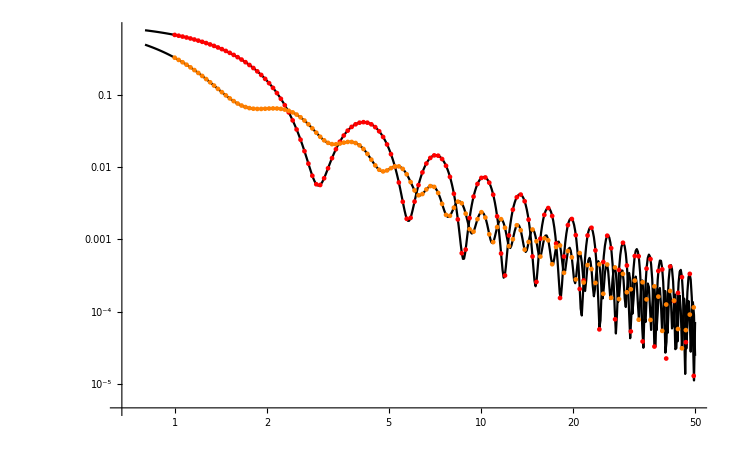

```mathematica
Clear[Term,Func1,Func2,DATA1,DATA2,OFILE,DATA1,DATA2]
Term[q_]=  Psicenter2hull Psicenter2surface//FullSimplify
FILE="PF_hull_surface.q";
OFILE="PF_hull2surface.dat";
DIRO1<>OFILE
Func1[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 1/.L-> 1.5,{θq,0,π/2}]
Func2[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 2/.L-> 0.5,{θq,0,π/2}]
SaveFunction[Func1,DIRO1<>OFILE,200,0.01,50];
SaveFunction[Func2,DIRO2<>OFILE,200,0.01,50];
DATA1={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
DATA2={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR2<>FILE,"Table"],1];
ListLogLogPlot[{DATA1,DATA2,{# ,Abs[Func1[#]]}&/@qq,{#,Abs[Func2[#]]}&/@qq},PlotStyle->{{Red,Thick},{Orange,Thick}, Black,Black},Joined-> {False,False,True,True}]
```

```mathematica
Solve[Collect[Integrate[Series[Term[q],{q,0,3}]Sin[θq],{θq,0,π/2}],q]==1-(q^2 sR2)/6,sR2]//Simplify
```

{{sR2→(L^3+2 L^2 R+12 L R^2+9 R^3)/(6 (L+R))}}

#### Phase factor surface to surface:

1/(q^2 (L+R)^2)4 (BesselJ[1,q R Sin[θq]] Cos[1/2 L q Cos[θq]] Csc[θq]+BesselJ[0,q R Sin[θq]] Sec[θq] Sin[1/2 L q Cos[θq]])^2

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidCylinder_mathematica_R1_L1.5/PF_surface2surface.dat

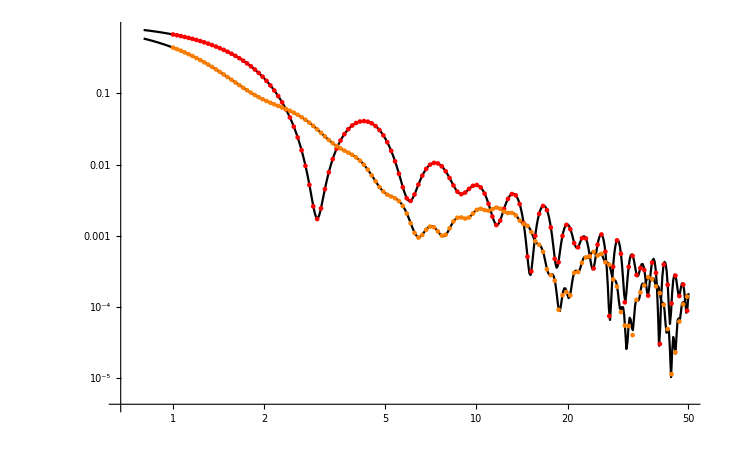

```mathematica
Clear[Term,Func1,Func2,DATA1,DATA2,OFILE,DATA1,DATA2]
Term[q_]=  Psicenter2surface Psicenter2surface//FullSimplify
FILE="PF_surface_surface.q";
OFILE="PF_surface2surface.dat";
DIRO1<>OFILE
Func1[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 1/.L-> 1.5,{θq,0,π/2}]
Func2[q_]:=NIntegrate[Term[q] Sin[θq]/.R-> 2/.L-> 0.5,{θq,0,π/2}]
SaveFunction[Func1,DIRO1<>OFILE,200,0.01,50];
SaveFunction[Func2,DIRO2<>OFILE,200,0.01,50];
DATA1={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
DATA2={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR2<>FILE,"Table"],1];
ListLogLogPlot[{DATA1,DATA2,{# ,Abs[Func1[#]]}&/@qq,{#,Abs[Func2[#]]}&/@qq},PlotStyle->{{Red,Thick},{Orange,Thick}, Black,Black},Joined-> {False,False,True,True}]
```

```mathematica
Solve[Collect[Integrate[Series[Term[q],{q,0,3}]Sin[θq],{θq,0,π/2}],q]==1-(q^2 sR2)/6,sR2]//Simplify
```

{{sR2→(L^3+3 L^2 R+12 L R^2+6 R^3)/(6 (L+R))}}